```mathematica
L1:=(-6 r^2 f[r]-3 r^3 f'[r]) NN'[r]+NN[r] (6 r-6 r f[r]-6 r^2 f'[r]-r^3 f''[r])-2 r^3 f[r] NN''[r]
```

```mathematica
L2:=(-4 f[r]+4 f[r]^2-6 r f'[r]+10 r f[r] f'[r]) NN'[r]+NN[r] (-4 f'[r]+4 f[r] f'[r]+2 r f'[r]^2-2 r f''[r]+2 r f[r] f''[r])+(-4 r f[r]+4 r f[r]^2) NN''[r]
```

```mathematica
L3:=1/r^3(-1+f[r]) (NN[r] (2+2 f[r]^2+6 r f'[r]+6 r^2 f'[r]^2-3 r^2 f''[r]+f[r] (-4-6 r f'[r]+3 r^2 f''[r]))+3 r (-3 r f'[r] NN'[r]+f[r] ((2+7 r f'[r]) NN'[r]-2 r NN''[r])-2 f[r]^2 (NN'[r]-r NN''[r])))
```

```mathematica
L=Collect[Simplify[(L1/3+(α/2)*L2+((α^2)/3)*L3)],{NN[r],NN'[r],NN''[r]}]
```

1/6 (-12 r^2 f[r]-(12 α^2 (-1+f[r]) f[r]^2)/r^2-6 r^3 f'[r]-(18 α^2 (-1+f[r]) f'[r])/r+(6 α^2 (-1+f[r]) f[r] (2+7 r f'[r]))/r^2+6 α (2 f[r]^2-3 r f'[r]+f[r] (-2+5 r f'[r]))) NN'[r]+1/6 NN[r] (-2 r (-6+6 f[r]+6 r f'[r]+r^2 f''[r])+6 α (2 (-1+f[r]) f'[r]+r f'[r]^2+r (-1+f[r]) f''[r])+1/r^3 2 α^2 (-1+f[r]) (2+2 f[r]^2+6 r f'[r]+6 r^2 f'[r]^2-3 r^2 f''[r]+f[r] (-4-6 r f'[r]+3 r^2 f''[r])))+1/6 (-4 r^3 f[r]+12 r α (-1+f[r]) f[r]-(12 α^2 (-1+f[r]) f[r])/r+(12 α^2 (-1+f[r]) f[r]^2)/r) NN''[r]

```mathematica
F0'[r_]:=Coefficient[L,NN[r]]
F1[r_]:=Coefficient[L,NN'[r]]
F2[r_]:=Coefficient[L,NN''[r]]
funcion2=Simplify[Integrate[F0'[r],r]-F1[r]+D[F2[r],r]]
```

(2 (3 r^4+α^2)-6 (r^4+r^2 α+α^2) f[r]+3 α (r^2+2 α) f[r]^2-2 α^2 f[r]^3)/(6 r^2)

```mathematica
f2=f[r]/. Solve[funcion2==μ,f[r],Reals][[1]]
```

Root[-6 r^4-2 α^2+6 r^2 μ+(6 r^4+6 r^2 α+6 α^2) #1+(-3 r^2 α-6 α^2) #1^2+2 α^2 #1^3&,1]

```mathematica
q2=ToRadicals[f2]==0
```

(r^2 α+2 α^2)/(2 α^2)-(9 r^4)/(2^(2/3) (-270 r^6 α^3-324 r^2 α^5-648 r^2 α^4 μ+√(78732 r^12 α^6+(-270 r^6 α^3-324 r^2 α^5-648 r^2 α^4 μ)^2))^(1/3))+((-270 r^6 α^3-324 r^2 α^5-648 r^2 α^4 μ+√(78732 r^12 α^6+(-270 r^6 α^3-324 r^2 α^5-648 r^2 α^4 μ)^2))^(1/3))/(6 2^(1/3) α^2)==0

```mathematica
Clear[α,μ]
```

```mathematica
α:=0.03
μ:=1
```

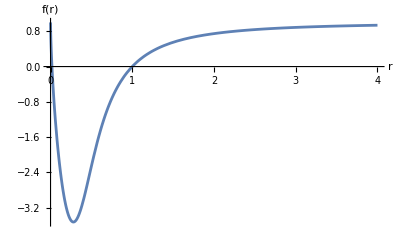

```mathematica
Plot[f2,{r,0,4},AxesLabel->{"r","f(r)"},PlotRange->All]
```

```mathematica
Solve[q2,r]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{r→-(√(3 μ-√3 √(-4 α^2+3 μ^2)))/(√6)},{r→(√(3 μ-√3 √(-4 α^2+3 μ^2)))/(√6)},{r→-(√(3 μ+√3 √(-4 α^2+3 μ^2)))/(√6)},{r→(√(3 μ+√3 √(-4 α^2+3 μ^2)))/(√6)}}

```mathematica
(√(3 μ-√3 √(-4 α^2+3 μ^2)))/(√6)
```

0.0173231

```mathematica
(√(3 μ+√3 √(-4 α^2+3 μ^2)))/(√6)
```

0.99985